## Energy Function - Contour Plots

```mathematica
ClearAll["Global`*"]
```

```mathematica
Tcore[I_,A1_,A2_,A3_]:=I/2(A1+A2)+A3*I^2;
Tsp[j_,A1_,A2_,A3_,V_,gm_]:=j/2(A2+A3)+A1*j^2-V*(2j-1)/(j+1)Sin[gm*π/180+π/6];
Aphi[phi_,A1_,A2_,A3_]:=A1*Cos[phi]^2+A2*Sin[phi]^2-A3;
Hmin[theta_,phi_,I_,j_,A1_,A2_,A3_,V_,gm_]:=I(I-1/2)Sin[theta]^2*Aphi[phi,A1,A2,A3]-2*A1*I*j*Sin[theta]+Tcore[I,A1,A2,A3]+Tsp[j,A1,A2,A3,V,gm];
```

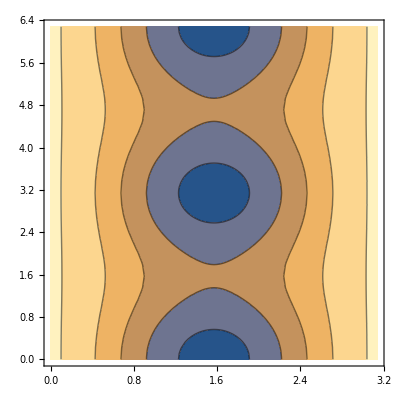

```mathematica
ContourPlot[Hmin[x,y,25/2,13/2,0.1,0.2,0.3,2.1,22],{x,0,π},{y,0,2π}]
```